## prel

```mathematica
Clear[eq,G,Λ1byτ,Λ2byτ,lhs1,lhs2,rhs1,rhs2,λ1,a1,h1,λ2,a2,h2,eqn1,eqn2,eqn3,eqn4];
(* redefining β-> 16 β S*)
G=βintra11((5-3 ctp^2)+(17 ctp-27 ctp^3) ct+(-3+9 ctp^2) ct^2+9 ctp (-3+5 ctp^2) ct^3) ;
Λ1byτ=λ1-h1+a1 ct+b1 ct^2+c1  ct^3;
lhs1=Λ1byτ+h1;rhs1=xintθpf1  G(λ1-h1+a1 ctp+b1 ctp^2+c1  ctp^3);
eq=lhs1-rhs1;
eqn1=SeriesCoefficient[eq,{ct,0,0}]//FullSimplify;
eqn2=SeriesCoefficient[eq,{ct,0,1}]//FullSimplify;
eqn3=SeriesCoefficient[eq,{ct,0,2}]//FullSimplify;
eqn4=SeriesCoefficient[eq,{ct,0,3}]//FullSimplify;
eqn1+ct eqn2+ct^2 eqn3+ct^3 eqn4==eq //FullSimplify

Clear[arr,array,cmat1,cmat2];arr=CoefficientArrays[{eqn1==0,eqn2==0,eqn3==0,eqn4==0},{λ1,a1,b1,c1}];
array=(Normal[arr]//FullSimplify)/.{ctp->ct};
cmat1=array[[1]]//Expand;
cmat2=array[[2]]//Expand;
Dimensions[cmat2];(*ct hst2*)
rep1={ct^2 h1 xintθpf1->hctsq1,ct^2 h2 xintθpf2->hctsq2,ct^3 h1 xintθpf1->hctcube1,ct^3 h2 xintθpf2->hctcube2,ct h1 xintθpf1->hct1,ct h2 xintθpf2->hct2,(******)h1 xintθpf1->hzero1,h2 xintθpf2->hzero2,ct^2 xintθpf1->ctsq1,ct^2 xintθpf2->ctsq2,ct^3 xintθpf1->ctcube1,ct^3 xintθpf2->ctcube2,ct^4 xintθpf1->ctquad1,ct^4 xintθpf2->ctquad2,ct^5 xintθpf1->ctfive1,ct^5 xintθpf2->ctfive2,ct^6 xintθpf1->ctsix1,ct^6 xintθpf2->ctsix2,ct xintθpf1->ct1,ct xintθpf2->ct2,ct h1 xintθpf1->hct1,ct h2 xintθpf2->hct2,xintθpf1->zero1,xintθpf2->zero2};
cmat1=(cmat1/.rep1);
cmat2=cmat2/.rep1;
MatrixForm[cmat1]//FullSimplify
MatrixForm[cmat2]//FullSimplify
```

True

(-3 hctsq1 βintra11+5 hzero1 βintra11
(17 hct1-27 hctcube1) βintra11
9 hctsq1 βintra11-3 hzero1 βintra11
9 (-3 hct1+5 hctcube1) βintra11)

(1+3 ctsq1 βintra11-5 zero1 βintra11 | -5 ct1 βintra11+3 ctcube1 βintra11 | (3 ctquad1-5 ctsq1) βintra11 | -5 ctcube1 βintra11+3 ctfive1 βintra11
-17 ct1 βintra11+27 ctcube1 βintra11 | 1+27 ctquad1 βintra11-17 ctsq1 βintra11 | -17 ctcube1 βintra11+27 ctfive1 βintra11 | -17 ctquad1 βintra11+27 ctsix1 βintra11
3 (-3 ctsq1+zero1) βintra11 | 3 (ct1-3 ctcube1) βintra11 | 1-9 ctquad1 βintra11+3 ctsq1 βintra11 | 3 (ctcube1-3 ctfive1) βintra11
9 (3 ct1-5 ctcube1) βintra11 | 9 (-5 ctquad1+3 ctsq1) βintra11 | 9 (3 ctcube1-5 ctfive1) βintra11 | 1+27 ctquad1 βintra11-45 ctsix1 βintra11)

## sigma for s=1/2

```mathematica
Clear[sig1,s,μ,B,v0];
sig1[B_,μ_,v0_,βintra11_]:=Block[{e=1,s,sm=0,sol0,sol2,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,kf2,f1,f2,vvec1,vvec2,vmm1,vmm2,vdotk1,vdotk2,conteq,h1,h2,λ1,a1,b1,c1,d1,g1,λ2,a2,b2,c2,d2,g2,cost,θp,Dphase1,Dphase2,vz1,vz2,cs,zero1,zero2,ct1,ct2,ctsq1,ctsq2,hzero1,hzero2,hct1,hct2,hctsq1,hctsq2,hctcube1,hctcube2,ctcube1,ctcube2,ctfive1,ctfive2,ctsix1,ctsix2,ctquad1 ,ctquad2,colvec,mat,sol,sol1,Λ1,Λ2,s1,s2,int1,int2},
(* band 1 *)
s=1/2;
kf1[θ_]=μ/(2 v0);
bc1[θ_]=-s/( kf1[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1 +e {0,0,B}.bc1[θ] (*-Graphics-*);
vvec1[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]={0,0,0};
vdotk1[θ_]=v0 s kf1[θ];
h1[θ_]=1/Dphase1[θ]( s v0 Cos[θ]+ e B(bc1[θ].(vvec1[θ]+vmm1[θ])) );
(*****************)

τ1[θ_]=((*(5-3 ctp^2)+(17 ctp-27 ctp^3) ct + (-3+9 ctp^2) ct^2+ 9 ctp (-3+5 ctp^2) ct^3 *)βintra11/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp](5-3 Cos[θp]^2),{θp,0,π}]+
(βintra11   Cos[θ])/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp](17-27 Cos[θp]^2),{θp,0,π}]+
(βintra11   Cos[θ]^2)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp](-3+9 Cos[θp]^2),{θp,0,π}]+
(9 βintra11  Cos[θ]^3)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp] (-3+5 Cos[θp]^2),{θp,0,π}])^-1;
(****************************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];

ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ctsq1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
ctcube1=Quiet[NIntegrate [f1[θp] Cos[θp]^3,{θp,0,π}]];
ctquad1 =Quiet[NIntegrate [f1[θp] Cos[θp]^4,{θp,0,π}]];
ctfive1=Quiet[NIntegrate [f1[θp] Cos[θp]^5,{θp,0,π}]];
ctsix1=Quiet[NIntegrate [f1[θp] Cos[θp]^6,{θp,0,π}]];
hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];
hctsq1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^2,{θp,0,π}]];
hctcube1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^3,{θp,0,π}]];
colvec=({{(-3 hctsq1+5 hzero1 )βintra11}, {(17 hct1-27 hctcube1) βintra11}, {9 hctsq1 βintra11-3 hzero1 βintra11}, {9 (-3 hct1+5 hctcube1) βintra11}});
mat=({{1+3 ctsq1 βintra11-5 zero1 βintra11, -5 ct1 βintra11+3 ctcube1 βintra11, (3 ctquad1-5 ctsq1) βintra11, -5 ctcube1 βintra11+3 ctfive1 βintra11}, {-17 ct1 βintra11+27 ctcube1 βintra11, 1+27 ctquad1 βintra11-17 ctsq1 βintra11, -17 ctcube1 βintra11+27 ctfive1 βintra11, -17 ctquad1 βintra11+27 ctsix1 βintra11}, {3 (-3 ctsq1+zero1) βintra11, 3 (ct1-3 ctcube1) βintra11, 1-9 ctquad1 βintra11+3 ctsq1 βintra11, 3 (ctcube1-3 ctfive1) βintra11}, {9 (3 ct1-5 ctcube1) βintra11, 9 (-5 ctquad1+3 ctsq1) βintra11, 9 (3 ctcube1-5 ctfive1) βintra11, 1+27 ctquad1 βintra11-45 ctsix1 βintra11}});
matr=mat.{λ1,a1,b1,c1};(* λ1 - h1+  a1 ct+b1 ct^2+c1  ct^3 *)
cs=(λ1 zero1-hzero1+a1 ct1+b1 ctsq1+c1 ctcube1);

sol2=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[4]]+colvec[[4]]==0,cs==0},{λ1,a1,b1,c1}],1];

sol=sol2;
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ]+b1 Cos[θ]^2+c1  Cos[θ]^3)/.sol;
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
s1=NIntegrate[int1[θ],{θ,0,π}];
{B,s1(*,MatrixRank[mat//Chop],sol0,sol1,MatrixForm[{λ1,a1,b1,c1}/.sol2]*)}
];
(* sig[B_,μ_,v0_,{βintra11_,βintra33_,βinter_}] *)
mu=10.0^-1;v0val= 6 10^-4;in=1;bval=1;in=1;
sig1[bval,mu,v0val,in]//Quiet
```

{1,8.03571×10^-9}

## sigma for s=3/2

```mathematica
Clear[sig2,s,μ,B,v0];
sig2[B_,μ_,v0_,βintra33_]:=Block[{e=1,s,sm=0,sol0,sol2,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,kf2,f1,f2,vvec1,vvec2,vmm1,vmm2,vdotk1,vdotk2,conteq,h1,h2,λ1,a1,b1,c1,d1,g1,λ2,a2,b2,c2,d2,g2,cost,θp,Dphase1,Dphase2,vz1,vz2,cs,zero1,zero2,ct1,ct2,ctsq1,ctsq2,hzero1,hzero2,hct1,hct2,hctsq1,hctsq2,hctcube1,hctcube2,ctcube1,ctcube2,ctfive1,ctfive2,ctsix1,ctsix2,ctquad1 ,ctquad2,colvec,mat,sol,sol1,Λ1,Λ2,s1,s2,int1,int2},

(* band 2 *)
s=3/2;
kf2[θ_]=μ/v0;
bc2[θ_]=(- s)/( kf2[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase2[θ_]=1 +e {0,0,B}.bc2[θ] ;
vvec2[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm2[θ_]={0,0,0};
vdotk2[θ_]=v0 s kf2[θ];
h2[θ_]=1/Dphase2[θ]( s v0 Cos[θ]+ e B(bc2[θ].(vvec2[θ]+vmm2[θ])) );

(* ***************************** *)

τ2[θ_]=((* (5-3 ctp^2)+(9 ctp-3 ctp^3) ct+(-3+9 ctp^2) ct^2+(-3 ctp+5 ctp^3) ct^3 *)βintra33/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp](5-3 Cos[θp]^2),{θp,0,π}]+
(3 βintra33  Cos[θ])/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp] (3-Cos[θp]^2),{θp,0,π}]+
(3βintra33  Cos[θ]^2)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp](-1+3 Cos[θp]^2),{θp,0,π}]+
(βintra33  Cos[θ]^3)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp] (-3+5 Cos[θp]^2),{θp,0,π}])^-1;
(****************************)
f2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]] Dphase2[θ] τ2[θ];
zero2=Quiet[NIntegrate [f2[θp],{θp,0,π}]];
ct2=Quiet[NIntegrate [f2[θp] Cos[θp],{θp,0,π}]];
ctsq2=Quiet[NIntegrate [f2[θp] Cos[θp]^2,{θp,0,π}]];
ctcube2 =Quiet[NIntegrate [f2[θp] Cos[θp]^3,{θp,0,π}]];
ctquad2 =Quiet[NIntegrate [f2[θp] Cos[θp]^4,{θp,0,π}]];
ctfive2=Quiet[NIntegrate [f2[θp] Cos[θp]^5,{θp,0,π}]];
ctsix2=Quiet[NIntegrate [f2[θp] Cos[θp]^6,{θp,0,π}]];

hzero2=Quiet[NIntegrate [f2[θp]h2[θp],{θp,0,π}]];
hct2=Quiet[NIntegrate [f2[θp]h2[θp]Cos[θp],{θp,0,π}]];
hctsq2=Quiet[NIntegrate [f2[θp]h2[θp] Cos[θp]^2,{θp,0,π}]];
hctcube2=Quiet[NIntegrate [f2[θp]h2[θp] Cos[θp]^3,{θp,0,π}]];


colvec=({{(-3 hctsq2 +5 hzero2 )βintra33}, {(9 hct2 -3 hctcube2) βintra33}, {(9 hctsq2-3 hzero2) βintra33}, {(-3 hct2+5 hctcube2) βintra33}});
mat=({{1+3 ctsq2 βintra33-5 zero2 βintra33, -5 ct2 βintra33+3 ctcube2 βintra33, (3 ctquad2-5 ctsq2) βintra33, -5 ctcube2 βintra33+3 ctfive2 βintra33}, {3 (-3 ct2+ctcube2) βintra33, 1+3 ctquad2 βintra33-9 ctsq2 βintra33, 3 (-3 ctcube2+ctfive2) βintra33, 3 (-3 ctquad2+ctsix2) βintra33}, {3 (-3 ctsq2+zero2) βintra33, 3 (ct2-3 ctcube2) βintra33, 1-9 ctquad2 βintra33+3 ctsq2 βintra33, 3 (ctcube2-3 ctfive2) βintra33}, {(3 ct2-5 ctcube2) βintra33, -5 ctquad2 βintra33+3 ctsq2 βintra33, (3 ctcube2-5 ctfive2) βintra33, 1+3 ctquad2 βintra33-5 ctsix2 βintra33}});
matr=mat.{λ2,a2,b2,c2};
cs=(λ2 zero2-hzero2+a2 ct2+b2 ctsq2+c2 ctcube2);


sol2=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[4]]+colvec[[4]]==0,cs==0},{λ2,a2,b2,c2}],1];

sol=sol2;

Λ2[θ_]=(λ2-h2[θ]+a2 Cos[θ]+b2 Cos[θ]^2+c2  Cos[θ]^3)/.sol;
int2[θ_]=-f2[θ]h2[θ]Λ2[θ];
s2=NIntegrate[int2[θ],{θ,0,π}];
{B,s2(*,MatrixRank[mat],(*MatrixForm[{λ2,a2,b2,c2}/.sol0],MatrixForm[{λ2,a2,b2,c2}/.sol1],*)MatrixForm[{λ2,a2,b2,c2}/.sol2]*)}
];
(* sig[B_,μ_,v0_,{βintra11_,βintra33_,βinter_}] *)
mu=10.0^-1;v0val= 6 10^-4;in=1;
sig2[0.01,mu,v0val,in]//Quiet
```

{0.01,1.6875×10^-7}

## sigma at B=0 for s=1/2

```mathematica
Clear[sig10,s,μ,B,v0];
sig10[μ_,v0_,βintra11_]:=Block[{e=1,B=0,s,sm,sol0,sol2,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,kf2,f1,f2,vvec1,vvec2,vmm1,vmm2,vdotk1,vdotk2,conteq,h1,h2,λ1,a1,b1,c1,d1,g1,λ2,a2,b2,c2,d2,g2,cost,θp,Dphase1,Dphase2,vz1,vz2,cs,zero1,zero2,ct1,ct2,ctsq1,ctsq2,hzero1,hzero2,hct1,hct2,hctsq1,hctsq2,hctcube1,hctcube2,ctcube1,ctcube2,ctfive1,ctfive2,ctsix1,ctsix2,ctquad1 ,ctquad2,colvec,mat,sol,sol1,Λ1,Λ2,s1,s2,int1,int2},
(* band 1 *)
s=1/2;sm=7/4;
kf1[θ_]=μ/v0;
bc1[θ_]=-s/( kf1[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1 ;
vvec1[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]={0,0,0};
vdotk1[θ_]=v0 s kf1[θ];
h1[θ_]=1/Dphase1[θ]( s v0 Cos[θ]);
(*****************)

τ1[θ_]=((*(5-3 ctp^2)+(17 ctp-27 ctp^3) ct + (-3+9 ctp^2) ct^2+ 9 ctp (-3+5 ctp^2) ct^3 *)βintra11/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp](5-3 Cos[θp]^2),{θp,0,π}]+
(βintra11   Cos[θ])/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp](17-27 Cos[θp]^2),{θp,0,π}]+
(βintra11   Cos[θ]^2)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp](-3+9 Cos[θp]^2),{θp,0,π}]+
(9 βintra11  Cos[θ]^3)/1 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp] (-3+5 Cos[θp]^2),{θp,0,π}])^-1;
(****************************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];

ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ctsq1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
ctcube1=Quiet[NIntegrate [f1[θp] Cos[θp]^3,{θp,0,π}]];
ctquad1 =Quiet[NIntegrate [f1[θp] Cos[θp]^4,{θp,0,π}]];
ctfive1=Quiet[NIntegrate [f1[θp] Cos[θp]^5,{θp,0,π}]];
ctsix1=Quiet[NIntegrate [f1[θp] Cos[θp]^6,{θp,0,π}]];
hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];
hctsq1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^2,{θp,0,π}]];
hctcube1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^3,{θp,0,π}]];
colvec=({{(-3 hctsq1+5 hzero1 )βintra11}, {(17 hct1-27 hctcube1) βintra11}, {9 hctsq1 βintra11-3 hzero1 βintra11}, {9 (-3 hct1+5 hctcube1) βintra11}});
mat=({{1+3 ctsq1 βintra11-5 zero1 βintra11, -5 ct1 βintra11+3 ctcube1 βintra11, (3 ctquad1-5 ctsq1) βintra11, -5 ctcube1 βintra11+3 ctfive1 βintra11}, {-17 ct1 βintra11+27 ctcube1 βintra11, 1+27 ctquad1 βintra11-17 ctsq1 βintra11, -17 ctcube1 βintra11+27 ctfive1 βintra11, -17 ctquad1 βintra11+27 ctsix1 βintra11}, {3 (-3 ctsq1+zero1) βintra11, 3 (ct1-3 ctcube1) βintra11, 1-9 ctquad1 βintra11+3 ctsq1 βintra11, 3 (ctcube1-3 ctfive1) βintra11}, {9 (3 ct1-5 ctcube1) βintra11, 9 (-5 ctquad1+3 ctsq1) βintra11, 9 (3 ctcube1-5 ctfive1) βintra11, 1+27 ctquad1 βintra11-45 ctsix1 βintra11}});
matr=mat.{λ1,a1,b1,c1};(* λ1 - h1+  a1 ct+b1 ct^2+c1  ct^3 *)
cs=(λ1 zero1-hzero1+a1 ct1+b1 ctsq1+c1 ctcube1);
(*sol0=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[3]]+colvec[[3]]==0,matr[[4]]+colvec[[4]]==0,cs==0},{λ1,a1,b1,c1}],1];

sol1=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[3]]+colvec[[3]]==0,matr[[4]]+colvec[[4]]==0},{λ1,a1,b1,c1}],1];*)

sol2=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[4]]+colvec[[4]]==0,cs==0},{λ1,a1,b1,c1}],1];

sol=sol2;
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ]+b1 Cos[θ]^2+c1  Cos[θ]^3)/.sol;
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
s1=NIntegrate[int1[θ],{θ,0,π}];
{B,s1(*,MatrixRank[mat//Chop],sol0,sol1,MatrixForm[{λ1,a1,b1,c1}/.sol2]*)}
];
(* sig[B_,μ_,v0_,{βintra11_,βintra33_,βinter_}] *)
mu=10.0^-1;v0val= 6 10^-4;in=1;bval=1;in=1;
sig10[mu,v0val,in]//Quiet
```

{0,8.03571×10^-9}

## sigma at B=0 for s=3/2

```mathematica
Clear[sig20,s,μ,B,v0];
sig20[μ_,v0_,βintra33_]:=Block[{e=1,B=0,s,sm,sol0,sol2,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,kf2,f1,f2,vvec1,vvec2,vmm1,vmm2,vdotk1,vdotk2,conteq,h1,h2,λ1,a1,b1,c1,d1,g1,λ2,a2,b2,c2,d2,g2,cost,θp,Dphase1,Dphase2,vz1,vz2,cs,zero1,zero2,ct1,ct2,ctsq1,ctsq2,hzero1,hzero2,hct1,hct2,hctsq1,hctsq2,hctcube1,hctcube2,ctcube1,ctcube2,ctfive1,ctfive2,ctsix1,ctsix2,ctquad1 ,ctquad2,colvec,mat,sol,sol1,Λ1,Λ2,s1,s2,int1,int2},

(* band 2 *)
s=3/2;sm=3/4;
kf2[θ_]=μ/(2v0);
bc2[θ_]=(- s)/( kf2[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase2[θ_]=1 ;
vvec2[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm2[θ_]={0,0,0};
vdotk2[θ_]=v0 s kf2[θ];
h2[θ_]=1/Dphase2[θ]( s v0 Cos[θ]+ e B(bc2[θ].(vvec2[θ]+vmm2[θ])) );

(* ***************************** *)

τ2[θ_]=((* (5-3 ctp^2)+(9 ctp-3 ctp^3) ct+(-3+9 ctp^2) ct^2+(-3 ctp+5 ctp^3) ct^3 *)βintra33/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp](5-3 Cos[θp]^2),{θp,0,π}]+
(3 βintra33  Cos[θ])/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp] (3-Cos[θp]^2),{θp,0,π}]+
(3βintra33  Cos[θ]^2)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp](-1+3 Cos[θp]^2),{θp,0,π}]+
(βintra33  Cos[θ]^3)/1 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp] (-3+5 Cos[θp]^2),{θp,0,π}])^-1;
(****************************)
f2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]] Dphase2[θ] τ2[θ];
zero2=Quiet[NIntegrate [f2[θp],{θp,0,π}]];
ct2=Quiet[NIntegrate [f2[θp] Cos[θp],{θp,0,π}]];
ctsq2=Quiet[NIntegrate [f2[θp] Cos[θp]^2,{θp,0,π}]];
ctcube2 =Quiet[NIntegrate [f2[θp] Cos[θp]^3,{θp,0,π}]];
ctquad2 =Quiet[NIntegrate [f2[θp] Cos[θp]^4,{θp,0,π}]];
ctfive2=Quiet[NIntegrate [f2[θp] Cos[θp]^5,{θp,0,π}]];
ctsix2=Quiet[NIntegrate [f2[θp] Cos[θp]^6,{θp,0,π}]];

hzero2=Quiet[NIntegrate [f2[θp]h2[θp],{θp,0,π}]];
hct2=Quiet[NIntegrate [f2[θp]h2[θp]Cos[θp],{θp,0,π}]];
hctsq2=Quiet[NIntegrate [f2[θp]h2[θp] Cos[θp]^2,{θp,0,π}]];
hctcube2=Quiet[NIntegrate [f2[θp]h2[θp] Cos[θp]^3,{θp,0,π}]];


colvec=({{(-3 hctsq2 +5 hzero2 )βintra33}, {(9 hct2 -3 hctcube2) βintra33}, {(9 hctsq2-3 hzero2) βintra33}, {(-3 hct2+5 hctcube2) βintra33}});
mat=({{1+3 ctsq2 βintra33-5 zero2 βintra33, -5 ct2 βintra33+3 ctcube2 βintra33, (3 ctquad2-5 ctsq2) βintra33, -5 ctcube2 βintra33+3 ctfive2 βintra33}, {3 (-3 ct2+ctcube2) βintra33, 1+3 ctquad2 βintra33-9 ctsq2 βintra33, 3 (-3 ctcube2+ctfive2) βintra33, 3 (-3 ctquad2+ctsix2) βintra33}, {3 (-3 ctsq2+zero2) βintra33, 3 (ct2-3 ctcube2) βintra33, 1-9 ctquad2 βintra33+3 ctsq2 βintra33, 3 (ctcube2-3 ctfive2) βintra33}, {(3 ct2-5 ctcube2) βintra33, -5 ctquad2 βintra33+3 ctsq2 βintra33, (3 ctcube2-5 ctfive2) βintra33, 1+3 ctquad2 βintra33-5 ctsix2 βintra33}});
matr=mat.{λ2,a2,b2,c2};
cs=(λ2 zero2-hzero2+a2 ct2+b2 ctsq2+c2 ctcube2);


sol2=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[4]]+colvec[[4]]==0,cs==0},{λ2,a2,b2,c2}],1];

sol=sol2;

Λ2[θ_]=(λ2-h2[θ]+a2 Cos[θ]+b2 Cos[θ]^2+c2  Cos[θ]^3)/.sol;
int2[θ_]=-f2[θ]h2[θ]Λ2[θ];
s2=NIntegrate[int2[θ],{θ,0,π}];
{B,s2}
];
mu=10.0^-1;v0val= 6 10^-4;in=1;
Quiet[sig20[mu,v0val,in]]
```

{0,1.6875×10^-7}

## data

```mathematica
mu=10.0^-1;v0val= 6 10^-4;in=1;rat=0.1;
x1=Quiet[sig10[mu,v0val,in]]
x2=Quiet[sig20[mu,v0val,in]]
list1=Sort[Join[{x1},Table[Quiet[sig1[B,mu,v0val,in]],{B,-105,105,10}]]]
list2=Sort[Join[{x2},Table[Quiet[sig2[B,mu,v0val,in]],{B,-105,105,10}]]]
```

{0,8.03571×10^-9}

{0,1.6875×10^-7}

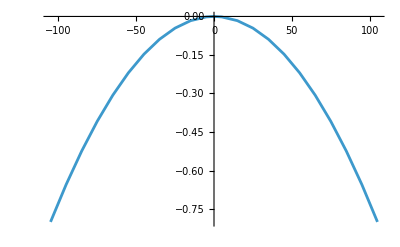

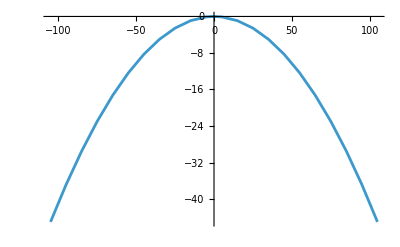

```mathematica
list={{-105,8.035071313714152*^-9},{-95,8.035187951734753*^-9},{-85,8.035292926290943*^-9},{-75,8.035386237276077*^-9},{-65,8.035467884595395*^-9},{-55,8.035537868165957*^-9},{-45,8.035596187916687*^-9},{-35,8.03564284378835*^-9},{-25,8.035677835733559*^-9},{-15,8.035701163716777*^-9},{-5,8.03571282771431*^-9},{0,8.035714285714275*^-9},{5,8.035712827714307*^-9},{15,8.035701163716775*^-9},{25,8.035677835733562*^-9},{35,8.035642843788353*^-9},{45,8.035596187916685*^-9},{55,8.035537868165956*^-9},{65,8.035467884595393*^-9},{75,8.03538623727608*^-9},{85,8.035292926290941*^-9},{95,8.035187951734755*^-9},{105,8.035071313714148*^-9}};
len=Length[list];
{x1,x2}={1/8.035714285714275*^-9,1/1.6874999999999955*^-7};
dat01=Table[{list[[i,1]],(Re[list[[i,2]]]x1 -1)10^4},{i,1,len}];
list={{-105,1.687424048622407*^-7},{-95,1.6874378265908867*^-7},{-85,1.6874502267849527*^-7},{-75,1.6874612491975207*^-7},{-65,1.6874708938222928*^-7},{-55,1.6874791606537587*^-7},{-45,1.6874860496871965*^-7},{-35,1.6874915609186687*^-7},{-25,1.6874956943450283*^-7},{-15,1.6874984499639124*^-7},{-5,1.687499827773749*^-7},{0,1.6874999999999955*^-7},{5,1.6874998277737488*^-7},{15,1.6874984499639124*^-7},{25,1.6874956943450278*^-7},{35,1.6874915609186685*^-7},{45,1.6874860496871965*^-7},{55,1.6874791606537587*^-7},{65,1.6874708938222928*^-7},{75,1.6874612491975204*^-7},{85,1.6874502267849533*^-7},{95,1.6874378265908867*^-7},{105,1.6874240486224068*^-7}};
dat02=Table[{list[[i,1]],(Re[list[[i,2]]]x2-1)10^6},{i,1,len}];
ListLinePlot[dat01]
ListLinePlot[dat02]
```

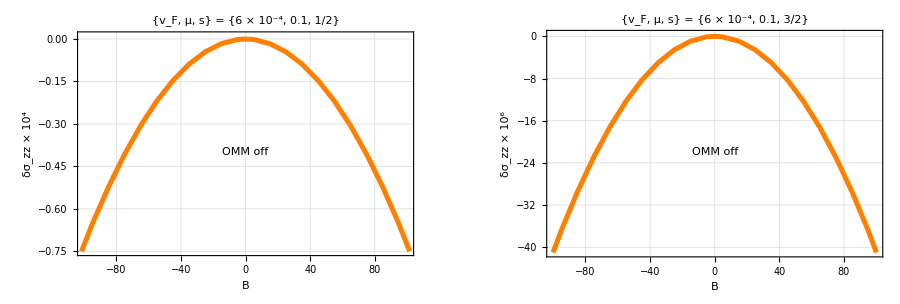

```mathematica
style={(*********)Directive[Orange,Thickness[0.008]]};

g1=ListPlot[{dat01},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-100,100},{-0.75,0.01}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,Axes->False,FrameLabel->{"B","δσ_zz × 10^4"},FrameTicksStyle->Directive[Bold,Black,12],PlotLabel->Style["{v_F, μ, s} = {6 × 10^-4, 0.1, 1/2}",Bold,Darker[Brown],18,FontFamily->"Times"],ImageSize->450,GridLines->Automatic,(*****)Epilog->{Style[Text["OMM off",{0,-0.4}],Blue,16,Bold,FontFamily->"Times"]}(*******)];

g2=ListPlot[{dat02},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-100,100},{-41,0.3}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,Axes->False,FrameLabel->{"B","δσ_zz × 10^6"},FrameTicksStyle->Directive[Bold,Black,12,FontFamily->"Times"],PlotLabel->Style["{v_F, μ, s} = {6 × 10^-4, 0.1, 3/2}",Bold,Darker[Brown],18,FontFamily->"Times"],ImageSize->450,GridLines->Automatic,(*****)Epilog->{Style[Text["OMM off",{0,-22}],Blue,16,Bold,FontFamily->"Times"]}(*******)];


pl=GraphicsGrid[{{g1,g2}},Spacings->{40,0},ImageSize->900]
SetDirectory[NotebookDirectory[]];
Export["sepnoomm.pdf",Rasterize[pl],ImageResolution->1000];
```